# Year 11 Curriculum

# Mathematica Bound-Reference

## Authored by gptreliance

Topic00

Functions + Relations (orientation content)

## Plotting with Asymptotes

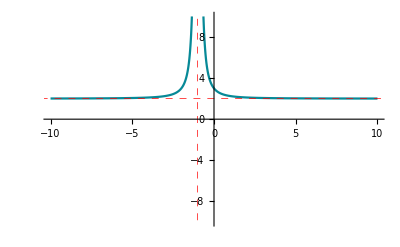

```mathematica
Plot[1/(x+1)^2+2,{x,-10,10},PlotRange->{-10,10},GridLines->{{-1},{2}},GridLinesStyle->Directive[Red, Dashed]]
```

Usage: Plot[equation,{x,x_start,x_end},PlotRange->{y_start,y_end},GridLines{{x_line},{y_line}},GridLinesStyle->Directive[colour,Dashed]]

## Plotting Relations (ContourPlot)

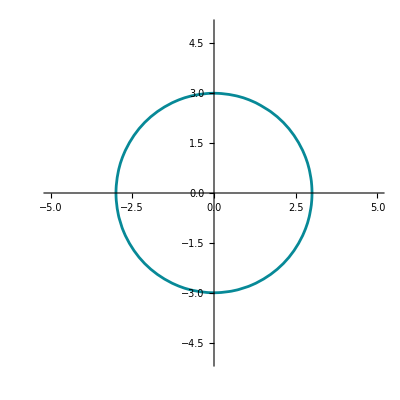

```mathematica
ContourPlot[x^2+y^2==9,{x,-5,5},{y,-5,5},Axes->True,Frame->False]
```

Usage: ContourPlot[equation, {x, x_start, x_end}, {y,y_start, y_end}, Axes->True, Frame->False]

## Plot - Restricted Domain

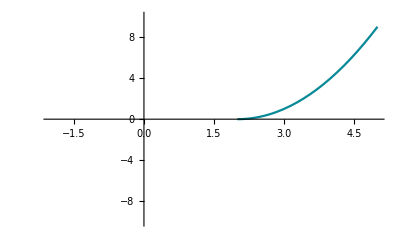

```mathematica
Plot[(x-2)^2&&x>=2,{x,-2,5},PlotRange->10]
```

Usage: Plot[expression && inequality {x, x_start, x_end}, PlotRange->range]

## Factorising and Expanding

```mathematica
FunctionDomain[1/(x+1)^2+2,x]
```

x<-1||x>-1

```mathematica
FunctionRange[1/(x+1)+2,x,y]
```

y<2||y>2

## Solving for x-intercepts

For the following statements, use double equals (==) similar to many programming languages for representing True.

Likewise, single equals (=) means assigning a value to a variable.

```mathematica
Solve[(2x+3)/4==-7,x]
```

{{x→-31/2}}

For the next one, remember to add a space between multiple variables. ax != a x, as ax is considered a variable.

```mathematica
Solve[a x+c==b x-d,x]
```

{{x→(-c-d)/(a-b)}}

```mathematica
Solve[a*x+c==b*x-d,x]
```

{{x→(-c-d)/(a-b)}}

Usage: Solve[expression_a == expression_b, x]

## Solving for y-intercepts

### Direct Substitution

You simply change the number.

```mathematica
4(0)+7
```

7

### Substitution Symbol

Using the /. symbol

```mathematica
4x+7/.x->0
```

7

### Define Function

Using the Function symbol

```mathematica
f[x_]:=4x+7
```

```mathematica
f[0]
```

7

## Reduce - Solve Inequalities

This combines fractions together by putting fractional expressions over a common denominator

Usage: Reduce[inequality, variable]

```mathematica
Reduce[(-2x+3)/4>=1,x]
```

x≤-1/2

## Troubleshooting Section (check at end of every lesson)

Remember to use a double equals (==) sign

Try to use Clear or ClearAll to remove accidental variable assigns

```mathematica
Clear[x]
```

Usage: Clear[some_variable_you_want_cleared], clears definitions

```mathematica
ClearAll[x,y,z]
```

Usage: ClearAll[some_variables_you_want_cleared], clears all associations, messages, values and associations

Remember, Solve command needs to know which variable needs to be found

e.g. Solve[50x-10==30x-20, x] <- That “x” needs to be stated

Variables are blue, commands are black and need to be in title case (e.g. Solve[])

Topic 01

Coordinate Geometry

## Solving for x-intercepts

For the following statements, use double equals (==) similar to many programming languages for representing True.

Likewise, single equals (=) means assigning a value to a variable.

```mathematica
Solve[(2x+3)/4==-7,x]
```

{{x→-31/2}}

For the next one, remember to add a space between multiple variables. ax != a x, as ax is considered a variable.

```mathematica
Solve[a x+c==b x-d,x]
```

{{x→(-c-d)/(a-b)}}

```mathematica
Solve[a*x+c==b*x-d,x]
```

{{x→(-c-d)/(a-b)}}

Usage: Solve[expression_a == expression_b, x]

## Simultaneous Equations

This places the equations into a single line, and uses x and y at the end to find what they are equal to.

```mathematica
Solve[{y==2x+1,y==-3x-7},{x,y}]
```

{{x→-8/5,y→-11/5}}

Usage: Solve[{simultaneous_a, simultaneous_b}, {variable_a, variable_b}]

## Converting to y=mx+c using Reduce[]

Putting y at the back ensures it finds what is equal to y.

```mathematica
Reduce[-2x+3y==10,y]
```

y==10/3+(2 x)/3

Usage: Reduce[equation, y]

## Solving Inequalities using Reduce[]

Only Reduce[] works for inequalities. Solve[] does not work.

```mathematica
Reduce[(-2x+3)/4>=1,x]
```

x≤-1/2

Usage: Reduce[equation, variable]

## Plotting y=mx+c

Place the expression into the first parameter. If there are multiple lines to be plotted, remember to use curly braces.

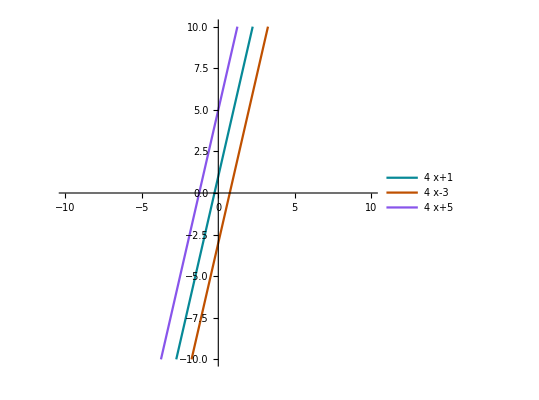

```mathematica
Plot[{4x+1,4x-3,4x+5},{x,-10,10},PlotRange->{-10,10},AspectRatio->Automatic,PlotLegends->"Expressions"]
```

## Plotting ax+by=c

### ContourPlot[] with the form ax+by=c

Use ContourPlot[] if you intend to keep it in its current form. As always, place the entire equation (with double equals) in the first parameter, and use curly braces for multiple.

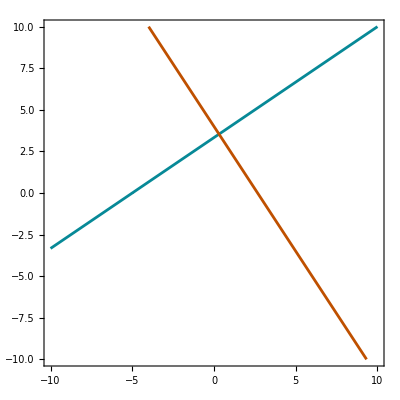

```mathematica
ContourPlot[{-2x+3y==10,-3x-2y+8==0},{x,-10,10},{y,-10,10},Axes->True]
```

### Rearranging ax+by=c into y=mx+c

Use the Reduce[] command to convert into y=mx+c

```mathematica
Reduce[-2x+3y==10,y]
```

y==10/3+(2 x)/3

Repeat the above steps for multiple equations.

```mathematica
Reduce[-3x-2y+8==0,y]
```

y==4-(3 x)/2

Finally, unleash the good’ol Plot[]

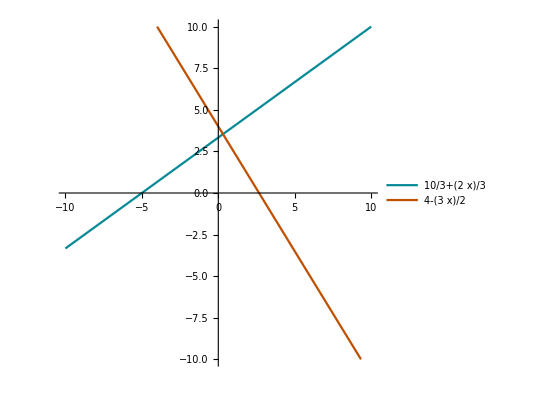

```mathematica
Plot[{10/3+(2 x)/3,4-(3 x)/2},{x,-10,10},PlotRange->{-10,10},AspectRatio->Automatic,PlotLegends->"Expressions"]
```

## Solving for y-intercepts

### Direct Substitution

You simply change the number.

```mathematica
4(0)+7
```

7

### Substitution Symbol

Using the /. symbol

```mathematica
4x+7/.x->0
```

7

### Define Function

Using the Function symbol

```mathematica
f[x_]:=4x+7
```

```mathematica
f[0]
```

7

## Finding the Gradient

Assuming m=tan(θ) (the theta symbol was obtained using Esc:theta:Esc)

```mathematica
Tan[67Degree]//N
```

2.35585

//N yields a number

## Finding the Angle

Assuming m=tan(θ)

```mathematica
ArcTan[7/6]/Degree//N
```

49.3987

//N yields a number

Topic 02

Probability and Counting Methods

Well there isn’t much here!

## Permutations (number of different rearrangements)

Permutations[] shows you the number of different possible ways to rearrange a list of objects.

```mathematica
Permutations[{cat,dog,pig}]
```

{{cat,dog,pig},{cat,pig,dog},{dog,cat,pig},{dog,pig,cat},{pig,cat,dog},{pig,dog,cat}}

## nPr - Length

This checks the number of different possible combinations available for a list of items.

However, you need to list the number of objects.

```mathematica
Length[Permutations[{cat,dog,pig,horse,fish},{2}]]
```

20

## nPr - Use Formula

Plugging in the values for nPr!

```mathematica
(5!)/((5-2)!)
```

20

## nCr - Binomial

```mathematica
Binomial[7,3]
```

35

## nCr - Use Formula

Plugging in the values for nCr!

```mathematica
(7!)/((7-3)!3!)
```

35

Topic 03

Quadratic Polynomials

## Finding the Turning Point

### FindMinimum and FindMaximum

```mathematica
FindMinimum[4 x^2+10x+7,x]
```

{0.75,{x→-1.25}}

Rationalize can be used from the front, or from the rear, to output the answer as exact values.

```mathematica
Rationalize[FindMinimum[4 x^2+10x+7,x]](*Front*)
```

{3/4,{x→-5/4}}

```mathematica
FindMinimum[4 x^2+10x+7,x]//Rationalize(*Rear*)
```

{3/4,{x→-5/4}}

FindMaximum[] example:

```mathematica
FindMaximum[-x^2+4x+3,x]//Rationalize
```

{7,{x→2}}

### Use -b/(2a) and Substituting

For example, Let y=5 x^2-7x-8

```mathematica
(-(-7))/(2(5))
```

7/10

Remember to use parenthesis for double negatives

This is bad: --7

This is good: -(-7)

```mathematica
5 x^2-7x-8/.x->7/10
```

-209/20

Therefore, TP = (7/10,209/20)

### Finding the Halfway Point Between 2 x-intercepts

Let y=5 x^2-7x-8

```mathematica
Solve[5 x^2-7x-8==0,x]
```

{{x→1/10 (7-√209)},{x→1/10 (7+√209)}}

```mathematica
(1/10 (7-√209)+1/10 (7+√209))/2//Simplify
```

7/10

```mathematica
5 x^2-7x-8/.x->7/10
```

-209/20

Therefore, T.P. = (7/10,-209/20)

### One Line Algorithm using Completing the Square

This is a single-line algorithm which takes as inputs the coefficients of a quadratic expression (and hence a is by definition non-zero) and returns as output the completed square form.

It leverages the creation of a user-created function which simplifies typing quire a bit.

```mathematica
compsq[a_,b_,c_]:=a(x+b/(2a))^2+c-b^2/(4a)//TraditionalForm
```

```mathematica
compsq[1,2,4]
```

(x+1)^2+3

## Discriminant

With known coefficients

```mathematica
Discriminant[10 x^2+3mx+7,x]
```

-40 (7+3 mx)

author’s note: this behaviour is indeed, strange.

```mathematica
9 m^2-(4*10*7)
```

-280+9 m^2

Usage: Discriminant[expression, variable]

With unknown coefficient

```mathematica
Discriminant[4 x^2+10x+7,x]
```

-12

Usage: Discriminant.14.14[expression, variable]

## Finding Quadratic Rules with Three Unknowns (check)

Assuming the quadratic goes through (1,-4), (-1,10) and (3,-2)

### Method 1

Define the function

```mathematica
f[x_]:=a x^2+b x+c
```

Solve

```mathematica
Solve[{f[1]==-4,f[-1]==10,f[3]==-2},{a,b,c}]
```

{{a→2,b→-7,c→1}}

### Method 2

Define the function

```mathematica
f[x_]:=a x^2+b x+c
```

Solve

```mathematica
Solve[f[{1,-1,3}]=={-4,10,-2},{a,b,c}]
```

{{a→2,b→-7,c→1}}

Therefore, y=2 x^2-7x+1

## Finding Quadratic Rules in Intercept Form

Example:

Find the equation of the quadratic which goes through the x-intercepts 2 and -3 and also goes through the point (4, 5)

```mathematica
(*y = a(x - x1) (x - x2)
Substitute in x-intercepts
Then substitute in known other points and solve for a*)
Solve[4==a(x-2)(x+3),a]/.x->5
```

{{a→1/6}}

Therefore y=1/6(x-2)(x+3)

## Plot Two Graphs on the one axes

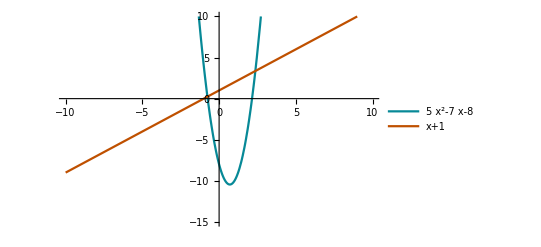

```mathematica
Plot[{5 x^2-7x-8,x+1},{x,-10,10},PlotRange->{-15,10},PlotLegends->"Expressions"]
```

## Points of Intersection

### Set both equations equal to one another which use x and y

Find the point of intersection between y=5 x^2-7x-8 and y=x+1

```mathematica
Solve[{y==5 x^2-7x-8,y==x+1},{x,y}]//TraditionalForm
```

{{x→1/5 (4-√61),y→1/5 (9-√61)},{x→1/5 (4+√61),y→1/5 (9+√61)}}

Therefore, POIs are:

(((4-√61)/5,(9-√61)/5),((4+√61)/5,(9+√61)/5))

Fancy shortcuts used: Ctrl+/ (Key for division) for fraction ((4-√61)/5), Ctrl+2 for square root (√61)

### Set both equations equal to one another and solve for x, then sub into either equation for y

Find the point of intersection between y=5 x^2-7x-8 and y=x+1

```mathematica
Solve[5 x^2-7x-8==x+1,x]
```

{{x→1/5 (4-√61)},{x→1/5 (4+√61)}}

```mathematica
x+1/.x->{{1/5 (4-√61)},{1/5 (4+√61)}}
```

{{1+1/5 (4-√61)},{1+1/5 (4+√61)}}

Therefore, POIs are:

(((4-√61)/5,(9-√61)/5),((4+√61)/5,(9+√61)/5))

## Solving x-intercepts

This is just a generic Solve[] command.

Remember to use a double equals == sign and to list the x parameter.

```mathematica
Solve[(2x+3)/4==-7,x]
```

{{x→-31/2}}

Remember to use a space “ ” to separate between two variables

```mathematica
Solve[a x+c==b x-d,x]
```

{{x→(-c-d)/(a-b)}}

```mathematica
Solve[a*x+c==b*x-d,x]
```

{{x→(-c-d)/(a-b)}}

Usage: Solve[expression == y, x]

Fancy shortcuts used: Ctrl+/ (Key for division) for fraction ((2x+3)/4)

## Solving y-intercepts

#### Using Direct Substitution

Simply substituting the unknown for a number.

```mathematica
4(0)+7
```

7

Usage: expression

#### Substitution Symbol (/.)

Using the /. method to replace x.

```mathematica
4x+7/.x->0
```

7

Usage: expression /. variable -> number

#### Define Function

This one employs the idea “f of x” into the working out.

The f[x_] tells Mathematica  that x is a variable that needs replacing

```mathematica
f[x_]:=4x+7
```

Using Shift+Enter saves this function and the value can be substituted by replacing x_ with a number shown below.

```mathematica
f[0]
```

7

Usage: F[variable_]:=expression, F[substitute]

## Reduce

This one solves inequalities. Solve[] does not work.

```mathematica
Reduce[(-2x+3)/4>=1,x]
```

x≤-1/2

## Factor

This one factorises expressions.

```mathematica
Factor[x^2+2x+1]
```

(1+x)^2

## Simplify

It simplifies. It is very effective on fractions.

```mathematica
Simplify[(a^2+b^2)/4-(a+b)^2/4]
```

-(a b)/2

Using it from the rear:

```mathematica
(a^2+b^2)/4-(a+b)^2/4//Simplify
```

-(a b)/2

## Expand

It expands. It is very useful on factorised expressions.

```mathematica
Expand[(1+x)^2]
```

1+2 x+x^2

Using TraditionalForm provides a more textbook-like output.

```mathematica
Expand[(1+x)^2]//TraditionalForm
```

x^2+2 x+1

Topic 04

Cubics and Quartics

## Polynomial Division

Using FullSimplify[] to yield simplified numbers and TraditionalForm to produce a textbook-like layout.

```mathematica
FullSimplify[(x^2+7x+11)/(x-2)]//TraditionalForm
```

x+29/(x-2)+9

PolynomialQuotientRemainder[] produces a remainder.

```mathematica
PolynomialQuotientRemainder[3 x^3+x-3,x-2,x]//TraditionalForm
```

{3 x^2+6 x+13,23}

Apart[] also works because it rewrites a rational expression as a sum of terms with minimal denominators, essentially splitting everything apart.

```mathematica
Apart[(x^2+7x+11)/(x-2)]//TraditionalForm
```

x+29/(x-2)+9

## Expanding a Factorised Cubic

Just use Expand[]

```mathematica
Expand[-(x-1)(x^2+4x+5)]//TraditionalForm
```

-x^3-3 x^2-x+5

## Equating Polynomials

If two polynomials are equal for all values of x we can use SolveAlways[LHS==RHS,variable]

SolveAlways[] always produces valid numbers because it simplifies all expressions to a number .

```mathematica
SolveAlways[2 x^3+x^2-7x+a==(x+2)(b x^2+c x-1),x]
```

{{a→-2,b→2,c→-3}}

This finds the values of any parameter such that the LHS=RHS for all values of the variable given. This is useful when given equivalent polynomials and need to find unknown constants.

## Plotting Cubics and Quartics

Just type in the expression. Plot[] will do all the work.

### Cubic

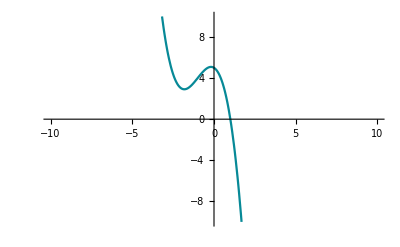

```mathematica
Plot[-x^3-3 x^2-x+5,{x,-10,10},PlotRange->{-10,10}]
```

### Quartic

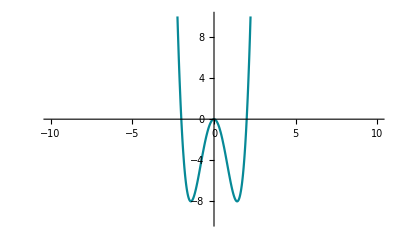

```mathematica
Plot[2 x^4-8 x^2,{x,-10,10},PlotRange->{-10,10}]
```

## Finding Local Minimum and Maximum by including a domain restriction

```mathematica
FindMaximum[{-x^3-3 x^2-x+5,-1<=x<=0},x]
```

{5.08866,{x→-0.183503}}

```mathematica
FindMinimum[{-x^3-3 x^2-x+5,-2<=x<=-1},x]
```

{2.91134,{x→-1.8165}}

## Finding Local minimum and Maximum by including an approximate value to the left of the turning point

```mathematica
FindMaximum[-x^3-3 x^2-x+5,{x,0}]
```

{5.08866,{x→-0.183503}}

```mathematica
FindMinimum[-x^3-3 x^2-x+5,{x,-1}]
```

{2.91134,{x→-1.8165}}

## Dividing expressions with remainder

PolynomialQuotientRemainder yields the remainder of the expression.

Usage: PolynomialQuotientRemainder[{expression},{divisor},{variable}]

```mathematica
PolynomialQuotientRemainder[x^3-3 x^2-6x+8,x-2,x]//TraditionalForm
```

{x^2-x-8,-8}

Topic 05

Function Relations and Inverses

This topic SUP is devoid of any Mathematica content. Enjoy your well deserved break!

Topic 06

Exponential and Logarithmic Functions

## Using Exponentials and Logs

### Logging with Euler’s Number ϵ

```mathematica
Log[ⅇ]
```

1

Fancy Shortcuts Used: Esc:ee:Esc for Euler’s Number ϵ

Alternatively, a capital e (E) can be used.

```mathematica
Log[E]
```

1

### Logging with Custom Bases

Using Log10 sets the base to 10.

```mathematica
Log10[10]
```

1

10 can be changed to any number for a different base.

```mathematica
Log2[2]
```

1

Alternatively, using Log[base,x] works just as well.

```mathematica
Log[5,x]
```

Log[x]/Log[5]

Fancy Shortcuts Used: Ctrl+/ for Fraction (Log[x]/Log[5])

## Plotting Exponentials with Horizontal Asymptotes

Use the Plot[] command with curly braces {} wherever multiple arguments are processed. The PlotRange command determines how much vertical space is shown.

### Using PlotStyle

PlotStyle denotes how the lines will be styled in respective order. Additional elements such as dashes can be included in a pair of curly braces {}.

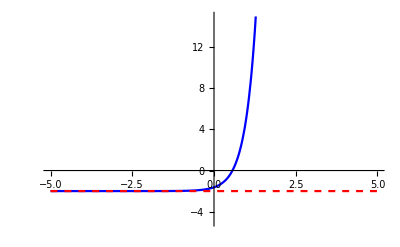

```mathematica
Plot[{ⅇ^(3x-1)-2,-2},{x,-5,5},PlotRange->{-5,15},PlotStyle->{Blue,{Red,Dashed}}]
```

Fancy Shortcuts Used: Esc:ee:Esc for Euler's Number ϵ

### Using GridLines

Usage: GridLines->{line_on_x_axis, line_on_y_axis}

GridLinesStyle->Directive[colour, style]

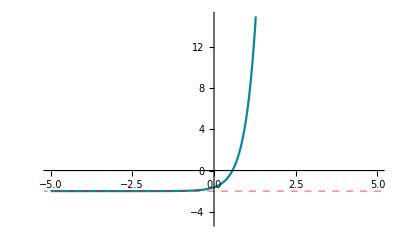

```mathematica
Plot[ⅇ^(3x-1)-2,{x,-5,5},PlotRange->{-5,15},GridLines->{None,{-2}},GridLinesStyle->Directive[Red,Dashed]]
```

Fancy Shortcuts Used: Esc:ee:Esc for Euler' s Number ϵ

## Plotting Logarithms with Vertical Asymptotes

Similar to GridLines from above, enter a value for the x-axis, but not y, because this is a vertical asymptote.

Don't include "y =" !

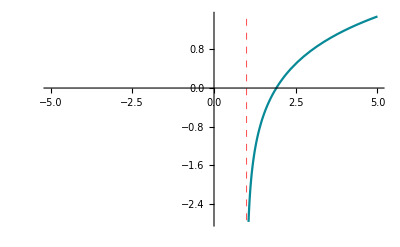

```mathematica
Plot[Log[3(x-1)]-1,{x,-5,5},GridLines->{{1},None},GridLinesStyle->Directive[Red,Dashed]]
```

## Solving Equations including Exponentials and Logarithms

It just solves.

Remember to include Reals to yield a real number.

### Without Reals

```mathematica
Solve[ⅇ^(3x-2)==4,x]
```

{{x→ConditionalExpression[1/3 (2+2 ⅈ π C[1]+Log[4]), C[1]∈ℤ]}}

### With Reals

```mathematica
Solve[ⅇ^(3x-2)==4,x,Reals]
```

{{x→2/3 (1+Log[2])}}

## Finding Inverse Functions

### Using Solve[]

Theoretically, Mathematica is supposed to find y automagically, however Mathematica does not want to solve it now. Refer to teacher screenshot beneath.

```mathematica
Solve[f[y]==x,y,Reals] (*please ignore this line and check the one beneath 👇*)
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[f[y]==x,y,ℝ]

Note: The conditional expression is just saying that there is a restriction on the function (x > -1)

### Using inbuilt functions

Theoretically, Mathematica is supposed to find y automagically, however Mathematica does not want to solve it now. This specific issue has also been documented by the teachers. Refer to teacher screenshot beneath.

```mathematica
f[x_]:=e^(2x-1)-1 (*don't look here*)
```

```mathematica
InverseFunction[f][x] (*look at the one below 👇*)
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

(Log[e]+Log[1+x])/(2 Log[e])

Topic 07

Circular Functions

This topic SUP is devoid of any Mathematica content. Enjoy your well deserved break!

Spares

## Spares

```mathematica
Manipulate[Plot[2 x^2+5x+k,{x,-5,5},PlotRange->10],{k,-5,5}]
```

```mathematica
PolynomialQuotientRemainder[x^3-2 x^2-4x+8,x-3,x]//TraditionalForm
```

{x^2+x-1,5}

```mathematica
Apart[(x^3-2 x^2-4x+8)/(x-3)]//TraditionalForm
```

x^2+x+5/(x-3)-1